Example of calculation of muon pair generation

**********************************************************************************************

1.Calculation of muon generation using 4 γ matrices (4*4) (conventional calculation)

f(s,u)；8 (t^2+u^2)

Scattering cross section of laboratory system (conventional calculation)；α^2/(4 s)+(α^2 Cos[θ]^2)/(4 s)

Total cross section integrated with respect to Θ；(4 π α^2)/(3 s)

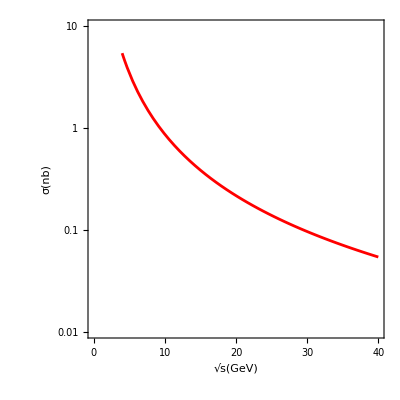

**********************************************************************************************

2.Muon pair generation calculation using γ matrix (256*256)

2.1.Calculation using 4 γ matrices (256*256) under Minkowski spacetime

Calculate the metric tensor as (-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

det (determinant of the metric tensor)=-1

f(s,u)；32768 (t^2+u^2)

Scattering cross section of laboratory system (consistent with conventional calculation results)；1/(75076 s)+Cos[θ]^2/(75076 s)

**********************************************************************************************

2.2.Trial calculation example using 16 γ matrices (256*256) in curved space-time

Calculate the metric tensor as (-1 | 1/9 | 1/9 | 1/9
1/9 | 10/9 | 1/9 | 1/9
1/9 | 1/9 | 10/9 | 1/9
1/9 | 1/9 | 1/9 | 10/9)

det(determinant of metric tensor)=-37/27

f(s,u)；(4096 (662920000 t^2+249852400 t u+661591653 u^2))/43046721

Scattering cross section in a laboratory system (trial calculation example using 16 γ matrices (256*256) for curved space)；(1574364053 α^2)/(5303360000 s)-(1328347 α^2 Cos[θ])/(2651680000 s)+(1074659253 α^2 Cos[θ]^2)/(5303360000 s)

Total cross section integrated with respect to Θ；(4223387359 π α^2)/(2983140000 s)

**********************************************************************************************

3.When using four γ matrices under Minkowski spacetime (conventional calculation) and γ matrix (256*256) under curved spacetime.
Comparison of trial calculation examples using 16 (trial calculation examples in this paper)

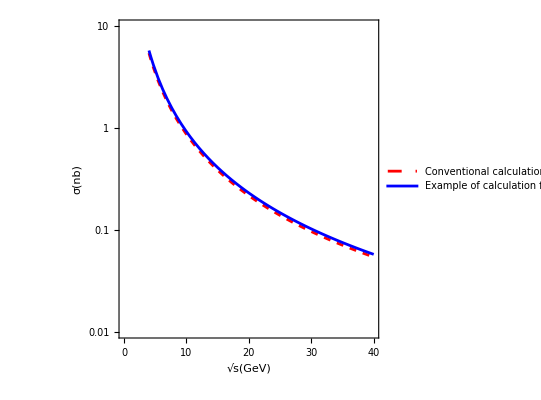

```mathematica
(*Title:Muon Pair Production Calculation (e⁺e⁻->μ⁺μ⁻) 
Author:[Hirokaxzu Maruyama] Date:January 2025 Version:1.0 Description:This code calculates the cross section for muon pair production in e⁺e⁻ collisions:1. Standard calculation using 4x4 gamma matrices 2. Extended formalism using 256x256 matrices 3. Implementation in both Minkowski and curved spacetime Physical Significance:-Basic QED process for lepton pair production-Important for particle accelerator physics-Test of lepton universality*)

(*Key Variables:s-total center-of-mass energy squared t,u-Mandelstam variables me-electron mass mμ-muon mass α-fine structure constant θ-scattering angle Energy Scales:√s-center-of-mass energy (GeV) σ-cross section (nb)*)

(*Step 1:Define matrix elements and spinor states*)(*Step 2:Calculate scattering amplitude*)(*Step 3:Compute differential cross section Note:Integration over angular variables gives total cross section*)(*Step 4:Plot cross section vs.center-of-mass energy Note:Shows characteristic 1/s behavior at high energies*)






Print[Style["Example of calculation of muon pair generation",Blue]];




Print["**********************************************************************************************"];
Print[Style["1.Calculation of muon generation using 4 γ matrices (4*4) (conventional calculation)",Blue]];

y1=.;
y2=.;
y3=.;
y4=.;
T1=.;
s=.;
t=.;
u=.;
(*γ matrix(4×4)*)

gu[0]={{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}};
gu[1]={{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
gu[2]={{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}};
gu[3]={{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};
e4=IdentityMatrix[4];

gd[0]=1*gu[0];
gd[1]=-gu[1];
gd[2]=-gu[2];
gd[3]=-gu[3];


sl[q]=gu[0]*q0+gu[1]*(-q1)+gu[2]*(-q2)+gu[3]*(-q3)+m*e4;
sl[p]=gu[0]*p0+gu[1]*(-p1)+gu[2]*(-p2)+gu[3]*(-p3)+m*e4;
sl[k]=gu[0]*k0+gu[1]*(-k1)+gu[2]*(-k2)+gu[3]*(-k3);
sl[j]=gu[0]*j0+gu[1]*(-j1)+gu[2]*(-j2)+gu[3]*(-j3);

s1=0;
s2=0;
y1=0;
me=m1*e4;
mμ=m*e4;
m=.;
m1=0;

For[x=0,x≤3,x++,
For[y=0,y≤3,y++,
s1=Tr[(sl[q]-me).gu[x].(sl[p]+me).gu[y]];
s2=Tr[(sl[k]+mμ).gd[x].(sl[j]-mμ).gd[y]];
y1=y1+s1*s2;
]];


(*Conversion using Mandelstam variables*)

m=0;
T1=Simplify[y1//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(u+m^2)/(2 Sqrt[u]),p3->(u-m^2)/(2 Sqrt[u]),z->1+s/(2 p3^2),s->2 m^2-u-t}];(*f(ut,u)*)


Print["f(s,u)；",T1];

keisuu =Coefficient[T1,t, 2];

y2=α^2/(2*s^3)*T1/keisuu;

t=-1/2*s*(1-Cos[θ]);
u=-1/2*s*(1+Cos[θ]);

Print["Scattering cross section of laboratory system (conventional calculation)；",Expand[y2]];

ya2=32/9*Integrate[y2,{θ,0,Pi}];

Print["Total cross section integrated with respect to Θ；",Expand[ya2]];


y3=32/9*Integrate[y2,{θ,0,Pi}]//.{s->sw^2};

xt=.;
yt=.;
xt[min_,max_,lbl_]:=Table[If[PossibleZeroQ@Mod[i,10],{i,If[lbl,i,Null],{0.04,0}},{i,Null,{0.02,0}}],{i,Ceiling[min],Floor[max],2}];
yt[min_,max_,lbl_]:=Join@@Table[Join[{{10^i,If[lbl,10^i,Null],{0.04,0}}},If[10^i<max,Table[{j 10^i,Null,{0.02,0}},{j,2,9}],{}]],{i,Log10[min],Log10[max]}];
xt1[min_,max_]:=xt[min,max,True];
xt0[min_,max_]:=xt[min,max,False];
yt1[min_,max_]:=yt[min,max,True];
yt0[min_,max_]:=yt[min,max,False];

α=1/137;
y4=y3*(10^6/2.57);
LogPlot[y4,{sw,4,40},PlotRange->{{0,40},{1/100,10}},PlotStyle->Red,Frame->True,FrameLabel->{Labeled[Sqrt[s],"(GeV)",Right],Labeled[σ,"(nb)",Right]},FrameTicks->{{yt1,yt0},{xt1,xt0}},AspectRatio->1]



Print["**********************************************************************************************"];
Print[Style["2.Muon pair generation calculation using γ matrix (256*256)",Blue]];

(*γ行列(256×256)*)

y10=.;
y20=.;
y30=.;
y40=.;
T10=.;
s=.;
t=.;
u=.;

(*Find 16 combinations of γ matrices (256*256) that satisfy the anti-commutative relationship*)
demoteRank4to2[y_]:=Flatten[Map[Flatten,Transpose[y,{1,3,2,4}],{2}],1];
pauli8times[g1_,g2_,g3_,g4_,g5_,g6_,g7_,g8_]:=demoteRank4to2[Outer[Times,demoteRank4to2[Outer[Times,demoteRank4to2[Outer[Times,g1,g2]],demoteRank4to2[Outer[Times,g3,g4]]]],demoteRank4to2[Outer[Times,demoteRank4to2[Outer[Times,g5,g6]],demoteRank4to2[Outer[Times,g7,g8]]]]]];

g[1]={{1,0},{0,-1}};
g[2]={{0,-I},{I,0}};
g[3]={{0,1},{1,0}};
g[0]={{1,0},{0,1}};

e256=IdentityMatrix[256];


γuv[0]=pauli8times[g[0],g[0],g[0],g[0],g[0],g[0],g[0],g[3]];
γuv[1]=I*pauli8times[g[0],g[0],g[0],g[0],g[3],g[2],g[2],g[2]];
γuv[2]=I*pauli8times[g[0],g[0],g[0],g[1],g[2],g[2],g[2],g[2]];
γuv[3]=I*pauli8times[g[0],g[0],g[3],g[2],g[2],g[2],g[2],g[2]];

γuv[4]=I*pauli8times[g[0],g[0],g[0],g[0],g[0],g[0],g[0],g[1]];
γuv[5]=I*pauli8times[g[0],g[0],g[0],g[0],g[0],g[0],g[3],g[2]];
γuv[6]=I*pauli8times[g[1],g[2],g[2],g[2],g[2],g[2],g[2],g[2]];
γuv[7]=I*pauli8times[g[0],g[0],g[1],g[2],g[2],g[2],g[2],g[2]];

γuv[8]=I*pauli8times[g[0],g[0],g[0],g[0],g[0],g[3],g[2],g[2]];
γuv[9]=I*pauli8times[g[0],g[0],g[0],g[0],g[0],g[0],g[1],g[2]];
γuv[10]=I*pauli8times[g[3],g[2],g[2],g[2],g[2],g[2],g[2],g[2]];
γuv[11]=I*pauli8times[g[0],g[0],g[0],g[0],g[1],g[2],g[2],g[2]];

γuv[12]=I*pauli8times[g[0],g[0],g[0],g[0],g[0],g[1],g[2],g[2]];
γuv[13]=I*pauli8times[g[0],g[1],g[2],g[2],g[2],g[2],g[2],g[2]];
γuv[14]=I*pauli8times[g[0],g[3],g[2],g[2],g[2],g[2],g[2],g[2]];
γuv[15]=I*pauli8times[g[0],g[0],g[0],g[3],g[2],g[2],g[2],g[2]];


num=115792089237316195423570985008687907853269984665640564039457584007913129639936;(*Confirm determinant*)


(*16 γ matrices (256×256) Calculation to confirm that the anticommutative relationship is satisfied*)
yg=0;
For[kh=0,kh≤15,kh++,
For[ks1=0,ks1≤15,ks1++,
yf=Det[γuv[kh].γuv[ks1]+γuv[ks1].γuv[kh]];
yg=yf+yg;
If[kh=!=ks1 && yf==num*16,Print["No.",km,",x=",kh,",y=",ks1]];
]];

If[kh==16&& ks1==16 && yg/num==16,Print[""],Print["γ matrix (256*256) 16 pieces Anti-commutation relation confirmation　NG"]];


(*Set metric tensor*)


Print[Style["2.1.Calculation using 4 γ matrices (256*256) under Minkowski spacetime",Blue]];

gd[0]=1;
gd[1]=1;
gd[2]=1;
gd[3]=1;
gd[4]=0;
gd[5]=0;
gd[6]=0;
gd[7]=0;
gd[8]=0;
gd[9]=0;
gd[10]=0;
gd[11]=0;
gd[12]=0;
gd[13]=0;
gd[14]=0;
gd[15]=0;

m256=1*m;


(*γ matrix multiplied by metric*)

For[km1=0,km1≤15,km1++,
γu[km1]=-gd[km1]*γuv[km1];
];


For[km2=0,km2≤15,km2++,
γd[km2]=1*γu[km2];
];
γd[0]=-1*γu[0];


metric={{-gd[0],gd[10],gd[12],gd[14]},{gd[11],gd[1],gd[4],gd[6]},{gd[13],gd[5],gd[2],gd[8]},{gd[15],gd[7],gd[9],gd[3]}}/gd[0];

Print["Calculate the metric tensor as ",MatrixForm[metric]];

Print["det (determinant of the metric tensor)=",Det[metric]];

sl[q]=γu[0]*q0+γu[1]*-q1+γu[2]*-q2+γu[3]*-q3+m256*e256;
sl[p]=γu[0]*p0+γu[1]*-p1+γu[2]*-p2+γu[3]*-p3+m256*e256;
sl[k]=γu[0]*k0+γu[1]*-k1+γu[2]*-k2+γu[3]*-k3;
sl[j]=γu[0]*j0+γu[1]*-j1+γu[2]*-j2+γu[3]*-j3;


s10=0;
s20=0;
y10=0;
me=m1*e256;
mμ=m*e256;
m=.;
m1=0;

For[x=0,x≤3,x++,
For[y=0,y≤3,y++,
s10=Tr[(sl[q]-me).γu[x].(sl[p]+me).γu[y]];
s20=Tr[(sl[k]+mμ).γd[x].(sl[j]-mμ).γd[y]];
y10=y10+s10*s20;
]];


(*Conversion using Mandelstam variables*)

m=0;
T10=Simplify[y10/gd[0]^8//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(u+m^2)/(2 Sqrt[u]),p3->(u-m^2)/(2 Sqrt[u]),z->1+s/(2 p3^2),s->2 m^2-u-t}];(*f(ut,u)*)


Print["f(s,u)；",T10];

keisuu =Coefficient[T10,t, 2];

y20=α^2/(2*s^3)*T10/keisuu;

t=-1/2*s*(1-Cos[θ]);
u=-1/2*s*(1+Cos[θ]);

Print["Scattering cross section of laboratory system (consistent with conventional calculation results)；",Expand[y20]];


y30=32/9*Integrate[y20,{θ,0,Pi}]//.{s->sw^2};

xt=.;
yt=.;
xt[min_,max_,lbl_]:=Table[If[PossibleZeroQ@Mod[i,10],{i,If[lbl,i,Null],{0.04,0}},{i,Null,{0.02,0}}],{i,Ceiling[min],Floor[max],2}];
yt[min_,max_,lbl_]:=Join@@Table[Join[{{10^i,If[lbl,10^i,Null],{0.04,0}}},If[10^i<max,Table[{j 10^i,Null,{0.02,0}},{j,2,9}],{}]],{i,Log10[min],Log10[max]}];
xt1[min_,max_]:=xt[min,max,True];
xt0[min_,max_]:=xt[min,max,False];
yt1[min_,max_]:=yt[min,max,True];
yt0[min_,max_]:=yt[min,max,False];




Print["**********************************************************************************************"];

Print[Style["2.2.Trial calculation example using 16 γ matrices (256*256) in curved space-time",Blue]];

y100=.;
y200=.;
y300=.;
y400=.;
T100=.;
s=.;
t=.;
u=.;
α=.;


gd[0]=9/10;
gd[1]=1;
gd[2]=1;
gd[3]=1;
gd[4]=1/10;
gd[5]=1/10;
gd[6]=1/10;
gd[7]=1/10;
gd[8]=1/10;
gd[9]=1/10;
gd[10]=1/10;
gd[11]=1/10;
gd[12]=1/10;
gd[13]=1/10;
gd[14]=1/10;
gd[15]=1/10;

m256=1*m;






(*γ matrix multiplied by metric*)

For[km1=0,km1≤15,km1++,
γu[km1]=-gd[km1]*γuv[km1];
];


For[km2=0,km2≤15,km2++,
γd[km2]=1*γu[km2];
];
γd[0]=-1*γu[0];


metric={{-gd[0],gd[10],gd[12],gd[14]},{gd[11],gd[1],gd[4],gd[6]},{gd[13],gd[5],gd[2],gd[8]},{gd[15],gd[7],gd[9],gd[3]}}/gd[0];

Print["Calculate the metric tensor as ",MatrixForm[metric]];

Print["det(determinant of metric tensor)=",Det[metric]];

sl[q]=γu[0]*q0+γu[1]*-q1+γu[2]*-q2+γu[3]*-q3+m256*e256;
sl[p]=γu[0]*p0+γu[1]*-p1+γu[2]*-p2+γu[3]*-p3+m256*e256;
sl[k]=γu[0]*k0+γu[1]*-k1+γu[2]*-k2+γu[3]*-k3;
sl[j]=γu[0]*j0+γu[1]*-j1+γu[2]*-j2+γu[3]*-j3;


s100=0;
s200=0;
y100=0;
me=m1*e256;
mμ=m*e256;
m=.;
m1=0;

For[x=0,x≤15,x++,
For[y=0,y≤15,y++,
s100=Tr[(sl[q]-me).γu[x].(sl[p]+me).γu[y]];
s200=Tr[(sl[k]+mμ).γd[x].(sl[j]-mμ).γd[y]];
y100=y100+s100*s200;
]];




(*Conversion using Mandelstam variables*)

m=0;
T100=Simplify[y100/gd[0]^8//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(u+m^2)/(2 Sqrt[u]),p3->(u-m^2)/(2 Sqrt[u]),z->1+s/(2 p3^2),s->2 m^2-u-t},TimeConstraint->5000];(*f(ut,u)*)


Print["f(s,u)；",T100];

keisuu =Coefficient[T100,t, 2];

y200=α^2/(2*s^3)*T100/keisuu;

t=-1/2*s*(1-Cos[θ]);
u=-1/2*s*(1+Cos[θ]);

Print["Scattering cross section in a laboratory system (trial calculation example using 16 γ matrices (256*256) for curved space)；",Expand[y200]];



ya20=32/9*Integrate[y200,{θ,0,Pi}];

Print["Total cross section integrated with respect to Θ；",Expand[ya20]];


y300=32/9*Integrate[y200,{θ,0,Pi}]//.{s->sw^2};

xt=.;
yt=.;
xt[min_,max_,lbl_]:=Table[If[PossibleZeroQ@Mod[i,10],{i,If[lbl,i,Null],{0.04,0}},{i,Null,{0.02,0}}],{i,Ceiling[min],Floor[max],2}];
yt[min_,max_,lbl_]:=Join@@Table[Join[{{10^i,If[lbl,10^i,Null],{0.04,0}}},If[10^i<max,Table[{j 10^i,Null,{0.02,0}},{j,2,9}],{}]],{i,Log10[min],Log10[max]}];
xt1[min_,max_]:=xt[min,max,True];
xt0[min_,max_]:=xt[min,max,False];
yt1[min_,max_]:=yt[min,max,True];
yt0[min_,max_]:=yt[min,max,False];



Print["**********************************************************************************************"];

α=1/137;
y40=y30*(10^6/2.57);
y400=y300*(10^6/2.57);

Print[Style["3.When using four γ matrices under Minkowski spacetime (conventional calculation) and γ matrix (256*256)\ under curved spacetime.
Comparison of trial calculation examples using 16 (trial calculation examples in this paper)",Blue]];
(*LogPlot[{y40,y400},{sw,4,40},PlotRange->{{0,40},{1/100,10}},PlotStyle->{{Red,Dashed},Blue},
PlotLegend->{"Before","After"},LegendPosition->{0.2,0.3},LegendSize->{0.6,0.4},LegendShadow->{.03,-.03},
Frame->True,FrameLabel->{Labeled[Sqrt[s],"(GeV)",Right],Labeled[σ,"(nb)",Right]},
FrameTicks->{{yt1,yt0},{xt1,xt0}},AspectRatio->1]*)

LogPlot[{y40,y400},{sw,4,40},PlotRange->{{0,40},{1/100,10}},PlotStyle->{{Red,Dashed},Blue},Frame->True,FrameTicks->{{yt1,yt0},{xt1,xt0}},
FrameLabel->{Labeled[Sqrt[s],"(GeV)",Right],Labeled[σ,"(nb)",Right]},
PlotLegends->Placed[LineLegend[Automatic,{"Conventional calculation","Example of calculation for this paper"},LabelStyle->8,
LegendFunction->"Frame",LegendLayout->"Column"],{{0.975,0.925},{1,0.9}}],AspectRatio->1]
```